## Import

```mathematica
mldir="/home/jwb/repos/github-research/csvs/Individuals/Pretty/ML/";
stackdir = "/home/jwb/repos/github-research/csvs/Individuals/Pretty/Stack/";
exportdir="/home/jwb/repos/github-research/MLMetrics/Frequency Analysis/";
```

```mathematica
data`raw=Import["/home/jwb/repos/github-research/csvs/Individuals/Pretty/ML/torch7-torch-commits.csv","Data"];
```

```mathematica
data`bigML=Import[#,"Data"]&/@FileNames["*.csv",mldir];
data`bigStack=Import[#,"Data"]&/@FileNames["*.csv",stackdir];
mlLabels={"Caffe","CNTK","DL4J","SystemML","TensorFlow","Theano","Torch7"};
stackLabels={"Cinder","Cloudstack","Glance","Horizon","Keystone","Neutron","Nova","Swift"};
```

## Functions

```mathematica
hist[set_,labels_,dir_]:=Table[Export[exportdir<>"Histograms/"<>dir<>labels[[n]]<>"Histogram.png",Histogram[Map[Total,set[[n]][[2;;]][[All,2;;]]],AxesLabel->{"People","Commits"},PlotLabel->labels[[n]],ImageSize->Large,LabelStyle->Directive[Bold]]],{n,Length@labels}];
```

```mathematica
fftShift[n_]:=RotateRight[Abs@Fourier[n],Floor@(Length[n]/2)]

fftPlot[n_]:=Rasterize@ListLinePlot[fftShift[n],PlotRange->Full,ImageSize->Large]

avgFFT[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
Mean@fft
]
avgFFTgeo[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
GeometricMean@fft
]

avgFFTnorm[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
(Mean@fft)/Total[tail,2]
]
avgFFTgeonorm[n_]:=Module[{tail,fft},
tail=n[[2;;]][[All,2;;]];
fft=fftShift/@tail;
(GeometricMean@fft)/Total[tail,2]
]

fftVis[n_,labels_]:=Rasterize@ListLinePlot[n,PlotRange->Full,ImageSize->Large, PlotLegends->labels]
```

## Example Single Repository

```mathematica
data`tail=data`raw[[2;;]][[All,2;;]];
data`fft=fftShift/@data`tail;
data`avgfft=Mean@data`fft;
fftVis[data`avgfft]
```

-Graphics-

```mathematica
fftVis[(data`avgfft)/Log[Total[data`tail,2]]]
```

-Graphics-

## Analysis

### Unnormalized Frequency Analysis

#### ML

```mathematica
fftVis[avgFFT/@data`bigML,mlLabels]
Export[exportdir<>"UnnormalizedML.png",%];
```

-Graphics-

#### Stack

```mathematica
fftVis[avgFFT/@data`bigStack,stackLabels]
Export[exportdir<>"UnnormalizedStack.png",%];
```

-Graphics-

### Normalized Analysis by Commits

#### ML

```mathematica
fftVis[avgFFTnorm/@data`bigML,mlLabels]
Export[exportdir<>"NormalizedML.png",%];
```

-Graphics-

#### Stack

```mathematica
fftVis[avgFFTnorm/@data`bigStack,stackLabels]
Export[exportdir<>"NormalizedStack.png",%];
```

-Graphics-

## Histogram Function

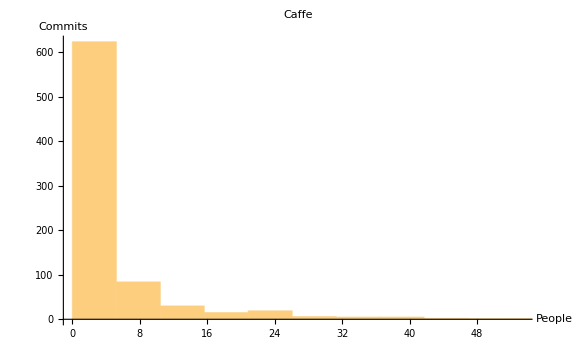
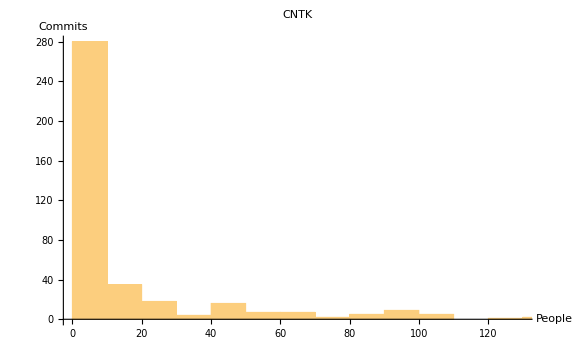
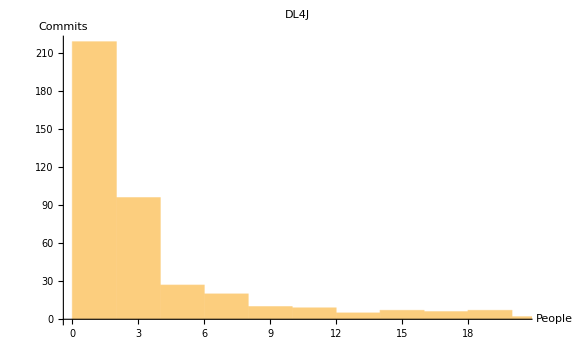
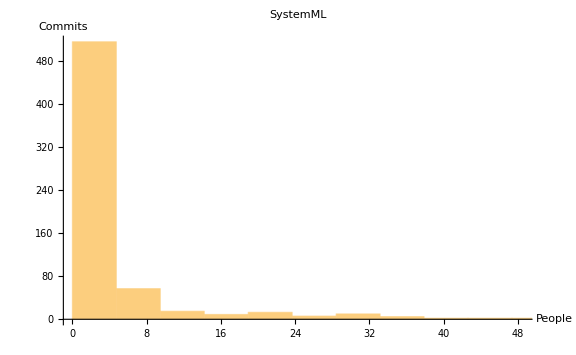
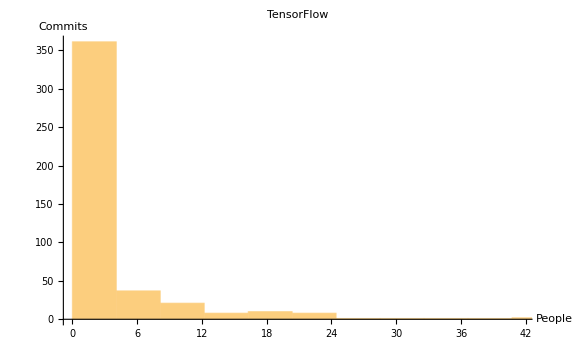
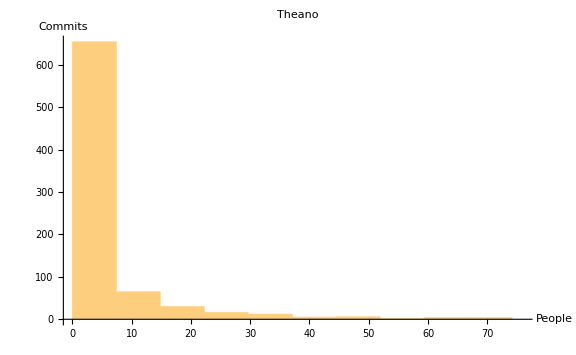
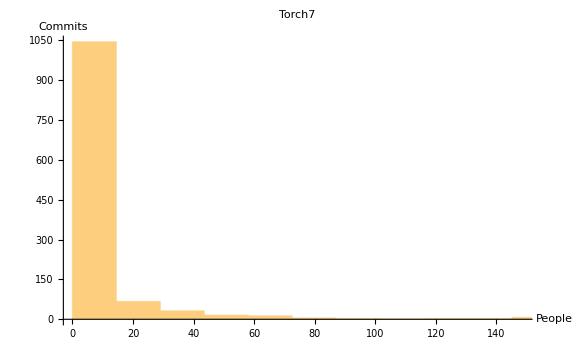

```mathematica
Table[Histogram[Map[Total,data`bigStack[[n]][[2;;]][[All,2;;]]],AxesLabel->{"People","Commits"},PlotLabel->mlLabels[[n]],ImageSize->Large,LabelStyle->Directive[Bold]],{n,Length@mlLabels}]
```

```mathematica
hist[data`bigML,mlLabels,"ML/"];
```

```mathematica
Table[Export[exportdir<>"Histograms/LongForm/"<>"Stack/"<>stackLabels[[n]]<>"Histogram.png",
ListLogPlot[
Sort[
Map[
Total,data`bigStack[[n]][[2;;]][[All,2;;]
]
],Greater
],PlotRange->Full,PlotLabel->stackLabels[[n]],AxesLabel->{"Index","Number of Commits"},ImageSize->Medium]
]
,{n,Length@stackLabels}];
```

```mathematica
Export[exportdir<>"Histograms/LongForm/Stack/FullRawHistogram.png",ListLogPlot[Table[
Sort[
Map[
Total,data`bigStack[[n]][[2;;]][[All,2;;]
]
],Greater
],{n,Length@stackLabels}],PlotRange->Full,PlotLegends->stackLabels,AxesLabel->{"Index","Number of Commits"},ImageSize->Large,Joined->True]]
```

/home/jwb/repos/github-research/MLMetrics/Frequency Analysis/Histograms/LongForm/Stack/FullRawHistogram.png